## DeMoivre’s Theorem and the Cost of Getting it Wrong

DeMoivre’s theorem is about variation in samples. The smaller the sample, the more the variation. If you don’t grasp this statistical truth, you’re bound to make a lot of mistakes.

Begin with the heights measured in inches of a population of 1,000 males.

```mathematica
pHeights = RandomVariate[NormalDistribution[68,10],1000];
```

By design, the population average should be 68 and the standard deviation should be 10 -- let’s check that to be sure.

```mathematica
stats1000 = {Mean[pHeights], StandardDeviation[pHeights], Min[pHeights], Max[pHeights]}
```

{68.766,9.92226,37.5138,97.7562}

The random error is

```mathematica
standardError1000 = stats1000[[2]]/Sqrt[1000]
```

0.31377

OK, that’s close enough. Now let’s randomly group the 1,000 students into 10 groups, each group having 100 students. Because the data is itself randomly selected from a Normal distribution, this is easily accomplished by partitioning the set into 10 smaller sets of 100. We’ll do this for smaller and larger sample sizes to get a feel for the variation.

## Variation for 10 sets of 100 students

```mathematica
s100 = Partition[pHeights,100];
```

```mathematica
s100[[2]]
```

{73.392,64.2352,75.1754,70.3077,69.5023,53.458,57.5432,73.0597,69.8269,65.2012,54.7397,52.758,67.4909,77.9912,61.3768,67.8729,59.7142,69.9547,71.5781,67.4315,82.7791,89.4937,65.2635,83.1962,57.79,76.4954,64.6436,81.3768,75.5858,56.2651,55.9563,72.6295,61.1828,70.9962,66.6353,66.5626,43.6882,59.8493,74.8112,55.4642,61.9682,86.6381,57.6656,65.8458,61.4448,75.8732,60.1062,56.7972,61.9328,72.2589,64.6701,62.3182,70.614,65.558,91.029,69.7464,67.9245,37.5138,76.0547,85.2224,71.6388,88.5022,74.3263,62.4507,78.2791,67.9995,77.8022,48.715,58.8991,69.1335,62.3377,60.1388,82.8457,78.3254,84.4086,52.6741,81.2381,57.0574,52.7622,65.3953,81.7967,70.027,74.6435,69.1442,65.1755,54.3111,71.0166,75.5435,73.5478,74.0258,89.4607,63.7675,79.1021,73.7153,92.5183,55.8487,71.7809,70.7865,81.2531,82.5579}

Now calculate the stats of each of the 10 100-sample groups:

```mathematica
stats100 = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s100
```

{{69.4732,10.2671,50.3642,97.7562},{68.7941,10.6874,37.5138,92.5183},{68.7835,10.3415,48.8344,92.369},{66.6563,9.72546,38.6679,89.3893},{68.9311,9.29724,44.7971,92.728},{68.2379,9.60782,39.9068,90.3524},{70.4188,9.88069,48.5441,94.0603},{69.447,10.0182,44.9927,96.0754},{68.8817,10.5447,43.4638,91.1373},{68.0361,8.67619,45.0554,86.4034}}

How do the stats of the 10 groups of 100 compare with those of the original group of 1,000 students?

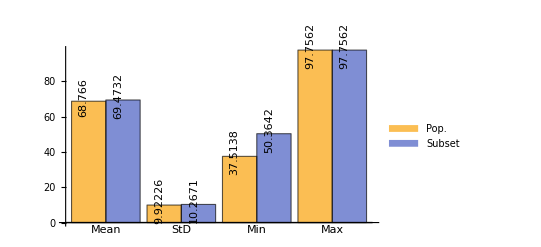
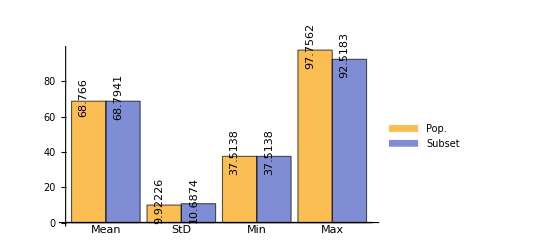
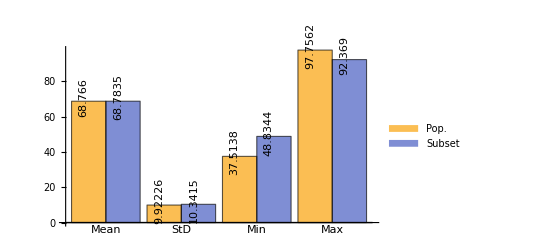
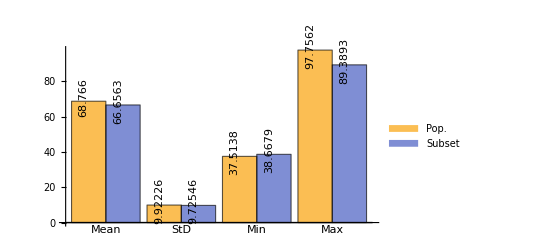
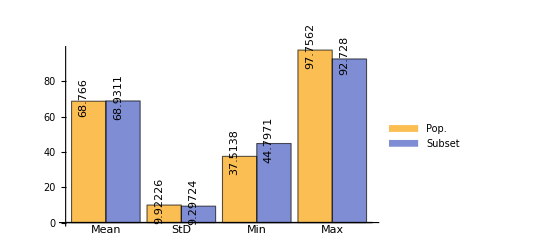
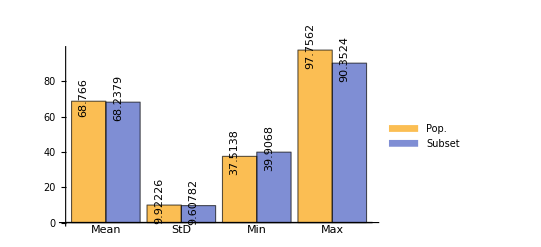
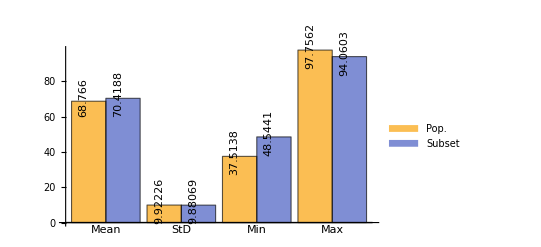
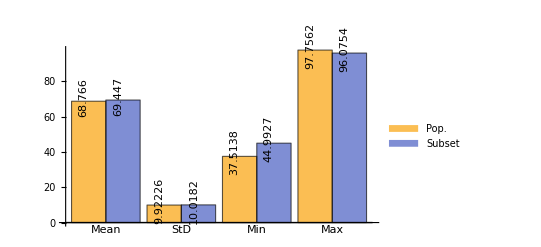

```mathematica
comp1000to100 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats100)
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

```mathematica
plotLabels = {"Mean", "Std. Dev.", "Min", "Max"};
```

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines10 = Transpose[Table[stats1000, 10]]
```

{{68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766},{9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226},{37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138},{97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562}}

Build the comparison plots

```mathematica
stats100Lines = Sort[#] & /@ Transpose[stats100]
```

{{66.6563,68.0361,68.2379,68.7835,68.7941,68.8817,68.9311,69.447,69.4732,70.4188},{8.67619,9.29724,9.60782,9.72546,9.88069,10.0182,10.2671,10.3415,10.5447,10.6874},{37.5138,38.6679,39.9068,43.4638,44.7971,44.9927,45.0554,48.5441,48.8344,50.3642},{86.4034,89.3893,90.3524,91.1373,92.369,92.5183,92.728,94.0603,96.0754,97.7562}}

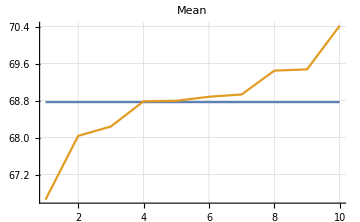
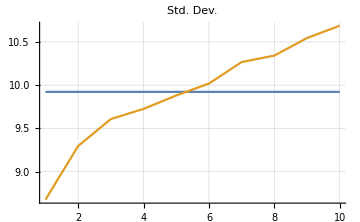
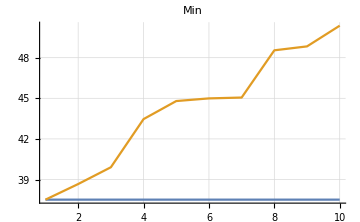
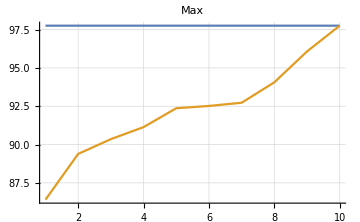

```mathematica
Table[ListLinePlot[{popLines10[[i]], stats100Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines10]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error”.

```mathematica
standardError100 = StandardDeviation[stats100[[All,1]]]
```

0.999992

## Variation for 20 sets of 50 students

```mathematica
s50 = Partition[pHeights,50];
```

```mathematica
s50[[2]]
```

{66.2487,65.166,64.4291,61.3348,68.9016,87.59,65.8039,76.2396,63.4374,76.0259,54.4067,65.5849,69.4216,69.8545,86.4293,63.5264,88.3181,63.9897,62.7014,63.7462,55.6046,81.2694,79.5968,80.1396,81.3872,78.2453,82.0924,78.5367,55.8857,66.7004,70.9992,64.2998,67.355,77.1096,97.7562,57.5935,64.3846,77.9137,51.2226,69.3286,81.1362,68.8901,71.1096,64.1702,76.1138,77.4694,76.9718,74.2197,57.3681,69.3488}

Now calculate the stats of each of the 20 50-sample groups:

```mathematica
stats50 = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s50
```

{{68.199,10.6655,50.3642,95.0974},{70.7475,9.7934,51.2226,97.7562},{66.8761,9.52438,43.6882,89.4937},{70.7121,11.5131,37.5138,92.5183},{69.1739,10.9871,48.8344,92.369},{68.3931,9.74928,50.2125,91.3224},{67.5397,10.9106,38.6679,89.3893},{65.7729,8.39445,47.7329,83.3262},{67.5682,10.0282,44.7971,92.728},{70.294,8.38373,48.8403,85.771},{68.7341,11.3477,39.9068,90.3524},{67.7417,7.56515,54.277,85.4636},{70.5486,10.5155,48.5458,93.7651},{70.2889,9.30801,48.5441,94.0603},{69.7227,9.83908,53.8049,96.0754},{69.1712,10.2866,44.9927,90.8045},{67.0389,10.207,43.4638,85.6645},{70.7245,10.6553,45.8043,91.1373},{67.2413,9.17281,45.0554,86.4034},{68.8309,8.16451,45.8981,84.7302}}

How do the stats of the 20 groups of 50 compare with those of the original group of 1,000 students?

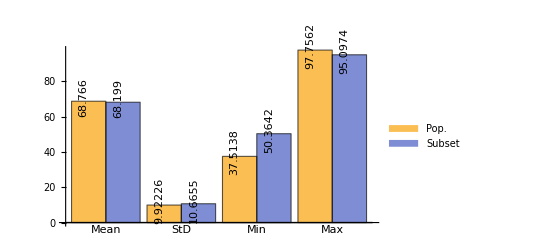
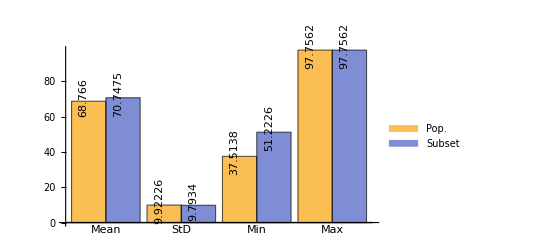
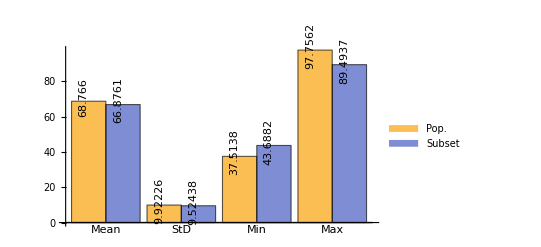
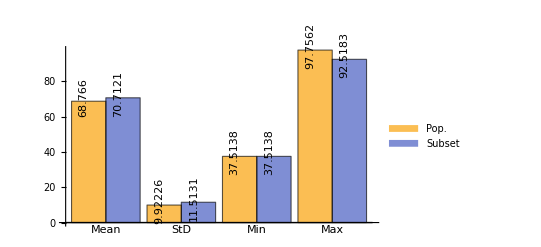
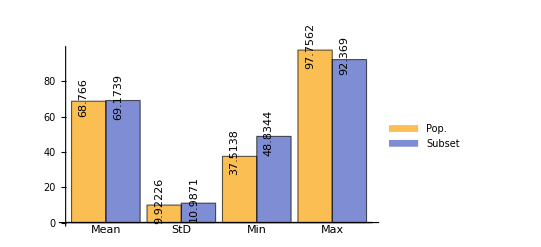
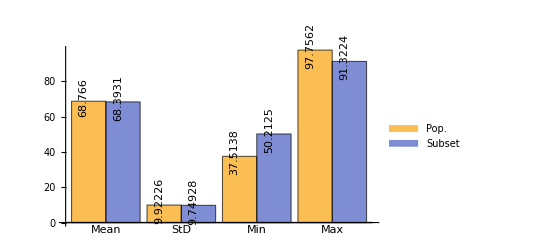
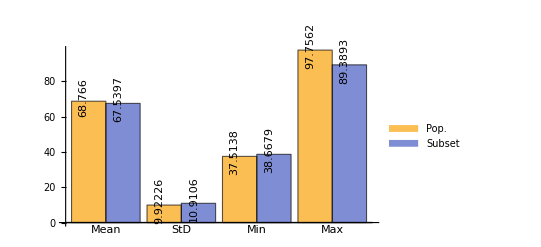
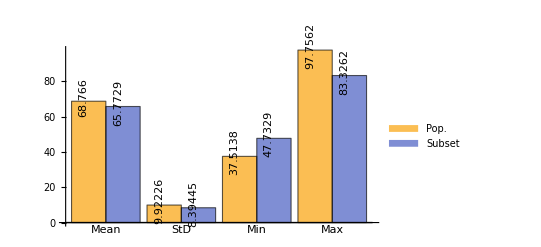

```mathematica
comp1000to50 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats50)
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines20 = Transpose[Table[stats1000, 20]]
```

{{68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766},{9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226},{37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138},{97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562}}

Build the comparison plots

```mathematica
stats50Lines = Sort[#] & /@ Transpose[stats50]
```

{{65.7729,66.8761,67.0389,67.2413,67.5397,67.5682,67.7417,68.199,68.3931,68.7341,68.8309,69.1712,69.1739,69.7227,70.2889,70.294,70.5486,70.7121,70.7245,70.7475},{7.56515,8.16451,8.38373,8.39445,9.17281,9.30801,9.52438,9.74928,9.7934,9.83908,10.0282,10.207,10.2866,10.5155,10.6553,10.6655,10.9106,10.9871,11.3477,11.5131},{37.5138,38.6679,39.9068,43.4638,43.6882,44.7971,44.9927,45.0554,45.8043,45.8981,47.7329,48.5441,48.5458,48.8344,48.8403,50.2125,50.3642,51.2226,53.8049,54.277},{83.3262,84.7302,85.4636,85.6645,85.771,86.4034,89.3893,89.4937,90.3524,90.8045,91.1373,91.3224,92.369,92.5183,92.728,93.7651,94.0603,95.0974,96.0754,97.7562}}

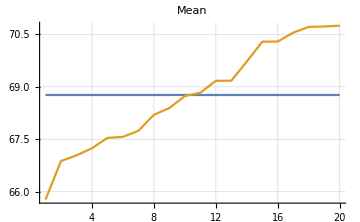
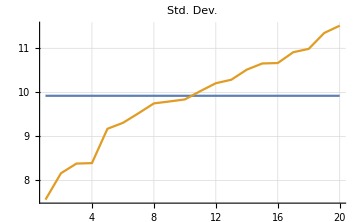
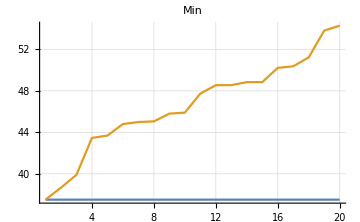
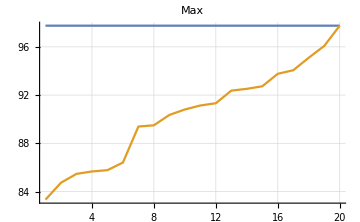

```mathematica
Table[ListLinePlot[{popLines20[[i]], stats50Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines20]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error”.

```mathematica
standardError50 = StandardDeviation[stats50[[All,1]]]
```

1.50295

## Variation for 50 sets of 20 students

```mathematica
s20 = Partition[pHeights,20];
```

```mathematica
s20[[2]]
```

{62.2528,95.0974,72.274,75.8632,60.0889,65.9547,57.907,70.5333,72.0266,61.0648,59.6041,77.2999,81.0201,74.4055,74.8181,87.2536,71.5399,60.5208,55.9174,62.159}

Now calculate the stats of each of the 50 20-sample groups:

```mathematica
stats20 = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s20
```

{{66.8145,11.1208,50.3642,81.2221},{69.8801,10.3856,55.9174,95.0974},{68.5617,9.41004,55.5413,90.5967},{71.3718,10.6555,54.4067,88.3181},{70.738,10.0831,51.2226,97.7562},{66.1305,7.35463,52.758,77.9912},{68.0332,11.6248,43.6882,89.4937},{67.5591,11.9637,37.5138,91.029},{68.7465,11.7204,48.715,88.5022},{73.5011,9.61343,54.3111,92.5183},{66.4268,10.9293,48.8344,85.5926},{70.6777,10.6614,54.9066,92.369},{69.3602,10.4881,51.8174,84.5476},{68.277,10.3292,50.2125,91.3224},{69.1758,9.85055,53.5433,83.9595},{69.0362,10.3895,53.8263,89.3893},{65.8136,13.0453,38.6679,87.0907},{66.8097,6.88464,52.9926,79.8524},{65.6258,8.26322,52.5736,79.9937},{65.996,9.52492,47.7329,83.3262},{65.8884,9.99641,50.1211,82.7162},{68.5195,9.34556,56.8951,92.728},{69.1794,10.791,44.7971,85.4931},{70.3458,6.6303,58.7716,82.0625},{70.7225,9.34042,50.3695,85.771},{69.647,13.8736,39.9068,90.3524},{68.5072,9.28012,48.3049,81.1347},{67.3735,8.25144,52.1074,84.1304},{71.5597,7.51008,54.8337,85.4636},{64.1022,6.73254,54.277,81.0757},{68.3954,11.2635,48.5458,87.9247},{72.4617,9.23915,52.9306,93.7651},{69.6463,10.4149,49.0342,88.6729},{70.5469,10.1333,48.5441,94.0603},{71.0435,8.69212,54.7714,87.329},{73.8704,9.43539,59.3094,96.0754},{67.9802,8.46444,53.8049,82.7766},{66.7949,9.0611,55.2448,83.5146},{67.5012,9.99175,52.9069,85.5673},{71.0882,11.9689,44.9927,90.8045},{67.945,9.94464,45.5874,84.7588},{67.4627,10.2028,48.8692,85.6645},{68.4323,11.3239,43.4638,91.1373},{67.9611,10.2741,45.8043,89.7879},{72.6075,11.1273,48.5672,90.2892},{69.3202,8.07364,49.7266,86.4034},{65.4139,8.18685,51.0448,80.8345},{68.7274,10.1406,45.0554,85.1026},{70.5867,8.05623,58.6994,84.7302},{66.1323,8.49382,45.8981,80.7829}}

How do the stats of the 50 groups of 200 compare with those of the original group of 1,000 students?

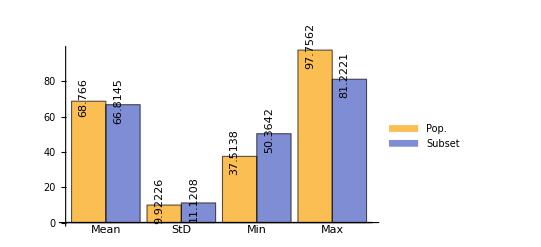
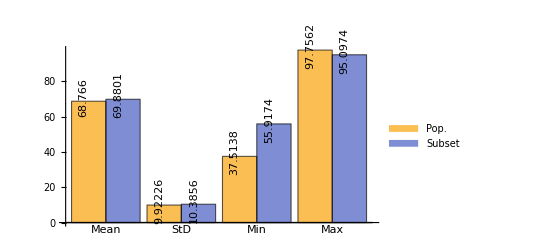
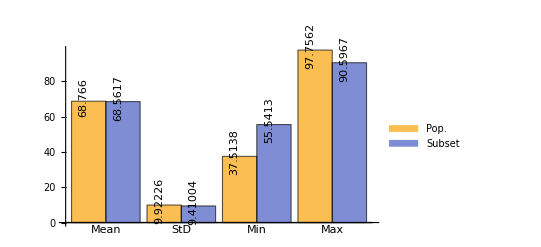
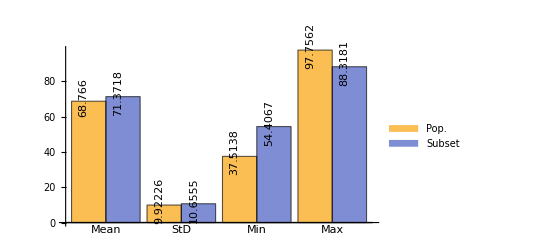
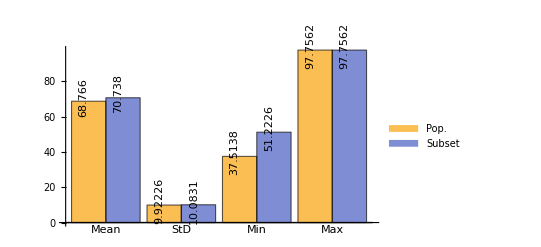
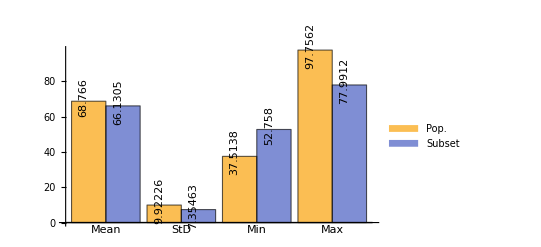
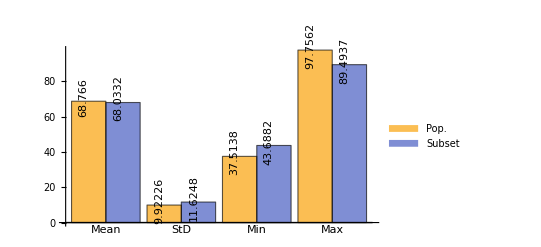
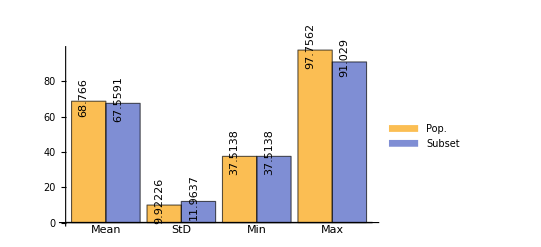

```mathematica
comp1000to20 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats20)
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines50 = Transpose[Table[stats1000, 50]]
```

{{68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766},{9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226},{37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138},{97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562}}

Build the comparison plots

```mathematica
stats20Lines = Sort[#] & /@ Transpose[stats20]
```

{{64.1022,65.4139,65.6258,65.8136,65.8884,65.996,66.1305,66.1323,66.4268,66.7949,66.8097,66.8145,67.3735,67.4627,67.5012,67.5591,67.945,67.9611,67.9802,68.0332,68.277,68.3954,68.4323,68.5072,68.5195,68.5617,68.7274,68.7465,69.0362,69.1758,69.1794,69.3202,69.3602,69.6463,69.647,69.8801,70.3458,70.5469,70.5867,70.6777,70.7225,70.738,71.0435,71.0882,71.3718,71.5597,72.4617,72.6075,73.5011,73.8704},{6.6303,6.73254,6.88464,7.35463,7.51008,8.05623,8.07364,8.18685,8.25144,8.26322,8.46444,8.49382,8.69212,9.0611,9.23915,9.28012,9.34042,9.34556,9.41004,9.43539,9.52492,9.61343,9.85055,9.94464,9.99175,9.99641,10.0831,10.1333,10.1406,10.2028,10.2741,10.3292,10.3856,10.3895,10.4149,10.4881,10.6555,10.6614,10.791,10.9293,11.1208,11.1273,11.2635,11.3239,11.6248,11.7204,11.9637,11.9689,13.0453,13.8736},{37.5138,38.6679,39.9068,43.4638,43.6882,44.7971,44.9927,45.0554,45.5874,45.8043,45.8981,47.7329,48.3049,48.5441,48.5458,48.5672,48.715,48.8344,48.8692,49.0342,49.7266,50.1211,50.2125,50.3642,50.3695,51.0448,51.2226,51.8174,52.1074,52.5736,52.758,52.9069,52.9306,52.9926,53.5433,53.8049,53.8263,54.277,54.3111,54.4067,54.7714,54.8337,54.9066,55.2448,55.5413,55.9174,56.8951,58.6994,58.7716,59.3094},{77.9912,79.8524,79.9937,80.7829,80.8345,81.0757,81.1347,81.2221,82.0625,82.7162,82.7766,83.3262,83.5146,83.9595,84.1304,84.5476,84.7302,84.7588,85.1026,85.4636,85.4931,85.5673,85.5926,85.6645,85.771,86.4034,87.0907,87.329,87.9247,88.3181,88.5022,88.6729,89.3893,89.4937,89.7879,90.2892,90.3524,90.5967,90.8045,91.029,91.1373,91.3224,92.369,92.5183,92.728,93.7651,94.0603,95.0974,96.0754,97.7562}}

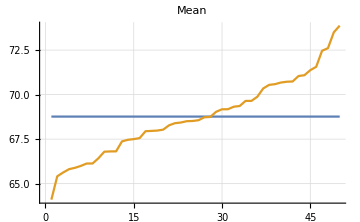
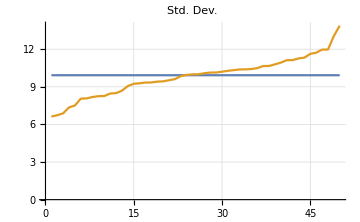
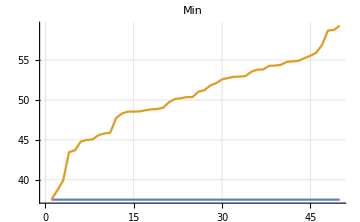
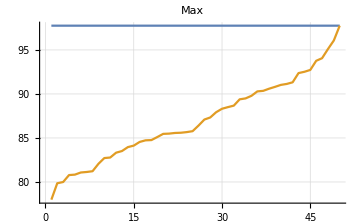

```mathematica
Table[ListLinePlot[{popLines50[[i]], stats20Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines50]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error” of the sampling mean.

```mathematica
standardError20 = StandardDeviation[stats20[[All,1]]]
```

2.18766

## Variation for 100 sets of 10 students

```mathematica
s10 = Partition[pHeights,10];
```

```mathematica
s10[[2]]
```

{78.6308,58.4575,64.2282,63.4365,79.3131,67.6203,51.9373,50.3642,79.7695,60.5086}

Now calculate the stats of each of the 50 20-sample groups:

```mathematica
stats10 = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s10
```

{{68.2024,11.7688,51.5403,81.2221},{65.4266,10.8766,50.3642,79.7695},{69.3063,10.9021,57.907,95.0974},{70.4538,10.3981,55.9174,87.2536},{67.6058,10.9361,55.5413,90.5967},{69.5177,8.0813,61.3348,87.59},{68.7979,10.6689,54.4067,88.3181},{73.9458,10.5425,55.6046,82.0924},{69.7963,12.746,51.2226,97.7562},{71.6798,7.08534,57.3681,81.1362},{67.1702,7.09471,53.458,75.1754},{65.0908,7.83927,52.758,77.9912},{73.2889,11.5516,56.2651,89.4937},{62.7776,9.51117,43.6882,74.8112},{66.0531,9.45761,56.7972,86.6381},{69.0651,14.4111,37.5138,91.029},{69.7746,11.2085,48.715,88.5022},{67.7183,12.7286,52.6741,84.4086},{70.9232,7.32508,54.3111,81.7967},{76.0791,11.2552,55.8487,92.5183},{68.7002,12.1628,48.8344,85.5926},{64.1534,9.63073,52.1805,77.68},{68.1453,12.0827,54.9066,92.369},{73.21,8.92861,59.5159,82.4126},{71.6603,11.6805,51.8174,84.5476},{67.0602,9.16694,54.1919,82.6719},{66.3698,9.43944,50.2125,82.2909},{70.1841,11.3161,57.3575,91.3224},{70.722,9.09298,53.5433,80.9652},{67.6295,10.8098,56.2196,83.9595},{68.8033,10.8896,53.8263,89.3893},{69.2691,10.4485,55.6119,88.6515},{62.9565,14.7453,38.6679,87.0907},{68.6707,11.1224,52.3444,86.5201},{67.9988,7.00931,55.2341,79.8524},{65.6206,6.91307,52.9926,77.5449},{67.9534,8.87334,52.5736,79.9937},{63.2982,7.30566,52.7272,74.7197},{68.8883,8.33175,55.6578,83.3262},{63.1038,10.1746,47.7329,75.4381},{63.1615,7.99786,50.1211,75.7703},{68.6152,11.4224,51.4459,82.7162},{67.7389,11.0757,57.002,92.728},{69.3001,7.76902,56.8951,81.071},{69.0254,11.8966,44.7971,85.4931},{69.3333,10.2102,48.8403,83.8387},{71.1988,7.60765,60.5613,82.0625},{69.4927,5.77174,58.7716,81.5929},{65.8869,7.83597,50.3695,76.6142},{75.5581,8.41519,58.4983,85.771},{68.8863,11.98,50.6407,88.2595},{70.4076,16.1721,39.9068,90.3524},{68.151,8.20771,51.2931,78.197},{68.8634,10.6847,48.3049,81.1347},{67.3622,10.4343,52.1074,84.1304},{67.3848,5.90446,59.9659,77.4973},{70.6056,6.12123,63.7212,82.4636},{72.5137,8.92062,54.8337,85.4636},{63.9592,5.29242,58.4787,76.4301},{64.2451,8.22408,54.277,81.0757},{66.9727,10.741,50.6814,80.4333},{69.8181,12.164,48.5458,87.9247},{70.264,6.19571,61.2215,78.3472},{74.6594,11.4494,52.9306,93.7651},{71.0289,11.6315,49.0342,88.6729},{68.2637,9.45808,52.1221,79.9824},{70.9829,8.90196,59.3131,86.5373},{70.1109,11.7093,48.5441,94.0603},{73.0295,7.61409,61.1318,87.329},{69.0575,9.63129,54.7714,81.6061},{69.3365,7.73472,59.3094,80.8234},{78.4044,9.07951,60.4219,96.0754},{68.3877,8.15852,56.4542,82.7766},{67.5726,9.1828,53.8049,78.7878},{64.9124,10.8248,55.2448,83.5146},{68.6773,6.94827,62.1891,83.3035},{67.628,9.96786,53.6594,81.9115},{67.3743,10.5532,52.9069,85.5673},{69.5985,11.3355,44.9927,85.56},{72.5778,13.,56.4711,90.8045},{69.2082,9.99086,54.9704,84.7588},{66.6817,10.2673,45.5874,76.7759},{69.1904,9.70571,51.5192,82.5239},{65.7351,10.9054,48.8692,85.6645},{64.3792,11.3398,43.4638,79.7212},{72.4855,10.2767,59.194,91.1373},{68.6114,9.60739,49.6815,81.6109},{67.3108,11.3842,45.8043,89.7879},{69.2249,10.7124,49.6608,90.2892},{75.9901,11.0095,48.5672,86.6809},{69.4838,6.38617,57.462,76.8223},{69.1566,9.83704,49.7266,86.4034},{64.1032,8.93473,53.3404,80.8345},{66.7245,7.60589,51.0448,77.3116},{66.7385,12.7156,45.0554,85.1026},{70.7163,6.82756,58.5171,80.033},{66.022,6.93724,58.6994,77.9254},{75.1514,6.52596,66.9293,84.7302},{65.9466,10.1035,45.8981,80.7829},{66.318,7.08158,54.2449,79.1351}}

How do the stats of the 50 groups of 200 compare with those of the original group of 1,000 students?

```mathematica
comp1000to10 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats10);
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines100 = Transpose[Table[stats1000, 100]]
```

{{68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766,68.766},{9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226,9.92226},{37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138,37.5138},{97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562,97.7562}}

Build the comparison plots

```mathematica
stats10Lines = Sort[#] & /@ Transpose[stats10]
```

{{62.7776,62.9565,63.1038,63.1615,63.2982,63.9592,64.1032,64.1534,64.2451,64.3792,64.9124,65.0908,65.4266,65.6206,65.7351,65.8869,65.9466,66.022,66.0531,66.318,66.3698,66.6817,66.7245,66.7385,66.9727,67.0602,67.1702,67.3108,67.3622,67.3743,67.3848,67.5726,67.6058,67.628,67.6295,67.7183,67.7389,67.9534,67.9988,68.1453,68.151,68.2024,68.2637,68.3877,68.6114,68.6152,68.6707,68.6773,68.7002,68.7979,68.8033,68.8634,68.8863,68.8883,69.0254,69.0575,69.0651,69.1566,69.1904,69.2082,69.2249,69.2691,69.3001,69.3063,69.3333,69.3365,69.4838,69.4927,69.5177,69.5985,69.7746,69.7963,69.8181,70.1109,70.1841,70.264,70.4076,70.4538,70.6056,70.7163,70.722,70.9232,70.9829,71.0289,71.1988,71.6603,71.6798,72.4855,72.5137,72.5778,73.0295,73.21,73.2889,73.9458,74.6594,75.1514,75.5581,75.9901,76.0791,78.4044},{5.29242,5.77174,5.90446,6.12123,6.19571,6.38617,6.52596,6.82756,6.91307,6.93724,6.94827,7.00931,7.08158,7.08534,7.09471,7.30566,7.32508,7.60589,7.60765,7.61409,7.73472,7.76902,7.83597,7.83927,7.99786,8.0813,8.15852,8.20771,8.22408,8.33175,8.41519,8.87334,8.90196,8.92062,8.92861,8.93473,9.07951,9.09298,9.16694,9.1828,9.43944,9.45761,9.45808,9.51117,9.60739,9.63073,9.63129,9.70571,9.83704,9.96786,9.99086,10.1035,10.1746,10.2102,10.2673,10.2767,10.3981,10.4343,10.4485,10.5425,10.5532,10.6689,10.6847,10.7124,10.741,10.8098,10.8248,10.8766,10.8896,10.9021,10.9054,10.9361,11.0095,11.0757,11.1224,11.2085,11.2552,11.3161,11.3355,11.3398,11.3842,11.4224,11.4494,11.5516,11.6315,11.6805,11.7093,11.7688,11.8966,11.98,12.0827,12.1628,12.164,12.7156,12.7286,12.746,13.,14.4111,14.7453,16.1721},{37.5138,38.6679,39.9068,43.4638,43.6882,44.7971,44.9927,45.0554,45.5874,45.8043,45.8981,47.7329,48.3049,48.5441,48.5458,48.5672,48.715,48.8344,48.8403,48.8692,49.0342,49.6608,49.6815,49.7266,50.1211,50.2125,50.3642,50.3695,50.6407,50.6814,51.0448,51.2226,51.2931,51.4459,51.5192,51.5403,51.8174,52.1074,52.1221,52.1805,52.3444,52.5736,52.6741,52.7272,52.758,52.9069,52.9306,52.9926,53.3404,53.458,53.5433,53.6594,53.8049,53.8263,54.1919,54.2449,54.277,54.3111,54.4067,54.7714,54.8337,54.9066,54.9704,55.2341,55.2448,55.5413,55.6046,55.6119,55.6578,55.8487,55.9174,56.2196,56.2651,56.4542,56.4711,56.7972,56.8951,57.002,57.3575,57.3681,57.462,57.907,58.4787,58.4983,58.5171,58.6994,58.7716,59.194,59.3094,59.3131,59.5159,59.9659,60.4219,60.5613,61.1318,61.2215,61.3348,62.1891,63.7212,66.9293},{74.7197,74.8112,75.1754,75.4381,75.7703,76.4301,76.6142,76.7759,76.8223,77.3116,77.4973,77.5449,77.68,77.9254,77.9912,78.197,78.3472,78.7878,79.1351,79.7212,79.7695,79.8524,79.9824,79.9937,80.033,80.4333,80.7829,80.8234,80.8345,80.9652,81.071,81.0757,81.1347,81.1362,81.2221,81.5929,81.6061,81.6109,81.7967,81.9115,82.0625,82.0924,82.2909,82.4126,82.4636,82.5239,82.6719,82.7162,82.7766,83.3035,83.3262,83.5146,83.8387,83.9595,84.1304,84.4086,84.5476,84.7302,84.7588,85.1026,85.4636,85.4931,85.56,85.5673,85.5926,85.6645,85.771,86.4034,86.5201,86.5373,86.6381,86.6809,87.0907,87.2536,87.329,87.59,87.9247,88.2595,88.3181,88.5022,88.6515,88.6729,89.3893,89.4937,89.7879,90.2892,90.3524,90.5967,90.8045,91.029,91.1373,91.3224,92.369,92.5183,92.728,93.7651,94.0603,95.0974,96.0754,97.7562}}

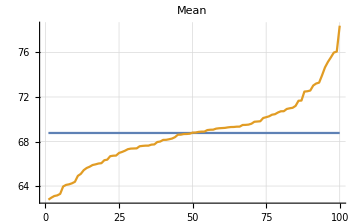
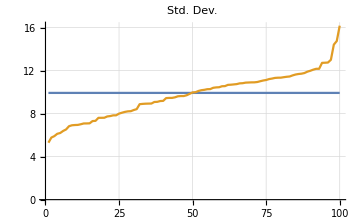
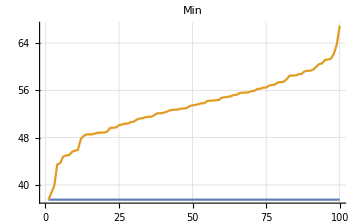
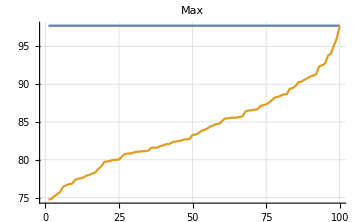

```mathematica
Table[ListLinePlot[{popLines100[[i]], stats10Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines100]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error” of the sampling mean.

```mathematica
standardError10 = StandardDeviation[stats10[[All,1]]]
```

3.05782

## Variation for 200 sets of 5 students (this is close to what William Sealey Gosset - aka “Student” was facing)

```mathematica
s5 = Partition[pHeights,5];
```

```mathematica
s5[[2]]
```

{59.9463,55.378,53.0251,74.2027,78.1266}

Now calculate the stats of each of the 50 20-sample groups:

```mathematica
stats5= {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s5;
```

How do the stats of the 50 groups of 200 compare with those of the original group of 1,000 students?

```mathematica
comp1000to5 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats5);
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines200 = Transpose[Table[stats1000, 200]];
```

Build the comparison plots

```mathematica
stats5Lines = Sort[#] & /@ Transpose[stats5];
```

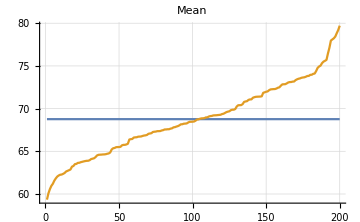
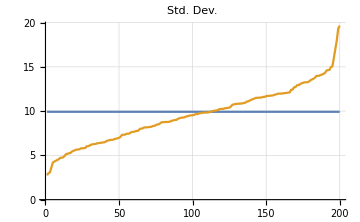
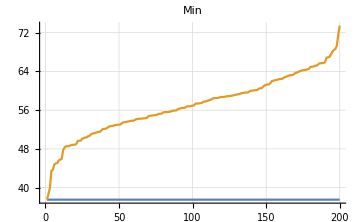
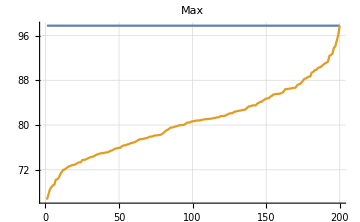

```mathematica
Table[ListLinePlot[{popLines200[[i]], stats5Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines200]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error” of the sampling mean.

```mathematica
standardError5 = StandardDeviation[stats5[[All,1]]]
```

4.23344

## Variation for 500 sets of 2 students

```mathematica
s2 = Partition[pHeights,2];
```

```mathematica
s2[[2]]
```

{73.925,78.4686}

Now calculate the stats of each of the 50 20-sample groups:

```mathematica
stats2 = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ s2;
```

How do the stats of the 50 groups of 200 compare with those of the original group of 1,000 students?

```mathematica
comp1000to2 = BarChart[#, LabelingFunction->(Placed[Rotate[#, 90°],Above]&), BarOrigin->Bottom,BarSpacing -> None, ChartLabels->{{"Mean", "StD", "Min", "Max"}, None}, ChartLegends-> Placed[{"Pop.","Subset"},Below]] & /@ (Transpose[{stats1000, #}] & /@ stats2);
```

And here’s another way to visualize the differences between the population statisitics and those of the subgroups.

First build the constant stats lines for the population - a series of the same values for mean, standard deviation, min, and max.

```mathematica
popLines500 = Transpose[Table[stats1000, 500]];
```

Build the comparison plots

```mathematica
stats2Lines = Sort[#] & /@ Transpose[stats2];
```

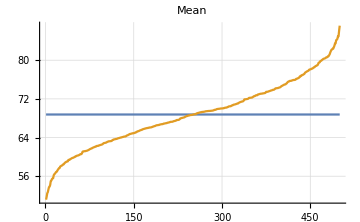
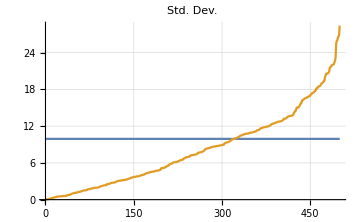
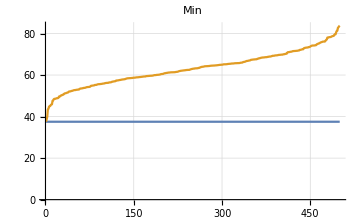
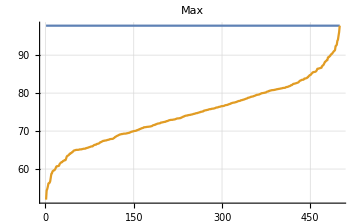

```mathematica
Table[ListLinePlot[{popLines500[[i]], stats2Lines[[i]]}, GridLines->Automatic, PlotRange->All, ImageSize->Medium, PlotLabel->plotLabels[[i]]], {i, 1, Length[popLines500]}]
```

And finally, what’s the standard deviation of the mean of the averages? This is the standard deviation of the sampling mean and is also known as the “standard error” of the sampling mean.

```mathematica
standardError2 = StandardDeviation[stats2[[All,1]]]
```

6.8169

Right, now that we have a feel, it’s time to pull it all together.

## A function for calculating the standard error of the mean

```mathematica
calcStandardError[populationValues_, sampleSize_]:= Module[{populationSize, samples,
popStats,sampleStats, 
sampleMeans, sampleStds, sampleMins, sampleMaxs,sampleStatsRanges,
stdError, deMoivreStdError, mistakenStdError},
(* Standard Error is the standard deviation of the sampling means *)

(* populationValues are the values of the random variable of interest for that population *)
(* There are no restrictions on the distribution of the random variable in the population -- it can be any distribution *)

populationSize = Length[populationValues];

(* INPUT CHECK *)
(* sampleSize must be less than or equal to the length of populationValues *)
If[sampleSize ≥  populationSize, Return["Please enter a sample size that is smaller than the population size and try again."]];
(* sampleSize cannot be less than 2 *)
If[sampleSize < 2, Return["Please enter a sample size that is greater than 1 and less than the population size and try again."]];

(* Calculate the population stats *)
popStats = {Mean[populationValues], StandardDeviation[populationValues], Min[populationValues], Max[populationValues]};

samples = Partition[populationValues, sampleSize];
(* For each sample, calculate the statistics *)
sampleStats = {Mean[#], StandardDeviation[#], Min[#], Max[#]} &/@ samples;

(* Pull together a list of all the sample means, all the sample standard derivations, etc. *)
{sampleMeans, sampleStds, sampleMins, sampleMaxs} = Transpose[sampleStats];

(* Calculate the standard error *)
stdError = StandardDeviation[sampleMeans];

(* What's the standard error according to DeMoivre's formula? *)
deMoivreStdError = StandardDeviation[populationValues]/Sqrt[sampleSize];

(* What's the naive or mistaken way to write the formula? This is the error that Howard Wainer claims that people were making for hundreds of years and are still making today *)
mistakenStdError = StandardDeviation[populationValues]/sampleSize;

(* We're also looking for the increase in variation or increase in range of all the stats as the sample sizes decrease *)
sampleStatsRanges = {Min[#], Max[#]} & /@ {sampleMeans, sampleStds, sampleMins, sampleMaxs};

{stdError, deMoivreStdError, mistakenStdError, sampleStatsRanges}

];
```

## Calculating the standard error of the sampling mean and comparing it with DeMoivre’s formula

If we start with our original population of 1000 heights that are Normally distributed with a population mean of 68 inches and a population standard deviation of 9.92, what happens to the standard error as the sample size decreases?

```mathematica
sampleSizes = {500, 250, 200, 100, 50, 25, 10, 5, 2};
```

```mathematica
stdErrors = calcStandardError[pHeights, #] & /@ sampleSizes
```

{{0.337048,0.443737,0.0198445,{{68.5276,69.0043},{9.76413,10.0821},{37.5138,39.9068},{96.0754,97.7562}}},{0.659806,0.627539,0.0396891,{{67.9136,69.4072},{9.57989,10.5438},{37.5138,43.4638},{91.1373,97.7562}}},{0.824371,0.70161,0.0496113,{{67.7199,69.9329},{9.43642,10.4585},{37.5138,44.9927},{91.1373,97.7562}}},{0.999992,0.992226,0.0992226,{{66.6563,70.4188},{8.67619,10.6874},{37.5138,50.3642},{86.4034,97.7562}}},{1.50295,1.40322,0.198445,{{65.7729,70.7475},{7.56515,11.5131},{37.5138,54.277},{83.3262,97.7562}}},{1.90851,1.98445,0.396891,{{65.5581,72.1965},{7.10519,13.1164},{37.5138,58.5171},{79.9937,97.7562}}},{3.05782,3.1377,0.992226,{{62.7776,78.4044},{5.29242,16.1721},{37.5138,66.9293},{74.7197,97.7562}}},{4.23344,4.43737,1.98445,{{59.3383,79.7128},{2.75389,19.6473},{37.5138,73.4512},{66.6571,97.7562}}},{6.8169,7.0161,4.96113,{{51.1507,87.1434},{0.0439273,28.3993},{37.5138,83.7661},{51.9373,97.7562}}}}

```mathematica
stdErrorsFromSampling = Transpose[{sampleSizes, stdErrors[[All,1]]}]
```

{{500,0.337048},{250,0.659806},{200,0.824371},{100,0.999992},{50,1.50295},{25,1.90851},{10,3.05782},{5,4.23344},{2,6.8169}}

```mathematica
stdErrorsFromDeMoivre = Transpose[{sampleSizes, stdErrors[[All,2]]}]
```

{{500,0.443737},{250,0.627539},{200,0.70161},{100,0.992226},{50,1.40322},{25,1.98445},{10,3.1377},{5,4.43737},{2,7.0161}}

```mathematica
stdErrorsMistake = Transpose[{sampleSizes, stdErrors[[All,3]]}]
```

{{500,0.0198445},{250,0.0396891},{200,0.0496113},{100,0.0992226},{50,0.198445},{25,0.396891},{10,0.992226},{5,1.98445},{2,4.96113}}

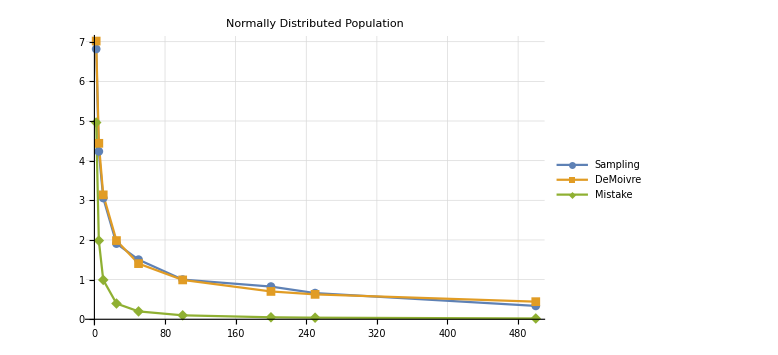

```mathematica
ListLinePlot[{stdErrorsFromSampling, stdErrorsFromDeMoivre, stdErrorsMistake}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"Sampling", "DeMoivre", "Mistake"}, Right], GridLines->Automatic,PlotLabel -> "Normally Distributed Population", ImageSize-> Large]
```

We see Demoivre’s formula is quite close to capturing reality while the mistaken notion of how standard error decreases makes things look a lot better than they really are. That’s the problem. If you don’t realize it’s DeMoivre’s formula, then you are susceptible of thinking that the error in a certain sample is quite low when in reality it is much higher than you think!

## Does the formula apply when the population is NOT normally distributed?

Let’s check.

```mathematica
pUniHeights =RandomVariate[ UniformDistribution[{37., 98.}],1000];
```

```mathematica
stdErrorsUni = calcStandardError[pUniHeights, #] & /@ sampleSizes
```

{{0.344324,0.780545,0.034907,{{67.1197,67.6066},{17.4242,17.4969},{37.1041,37.1157},{97.8164,97.8797}}},{1.48185,1.10386,0.0698141,{{65.3385,68.9009},{17.0562,17.8187},{37.1041,37.8014},{97.1984,97.8797}}},{0.950499,1.23415,0.0872676,{{66.5405,68.6014},{15.9656,18.0498},{37.1041,37.6537},{97.1984,97.8797}}},{1.78116,1.74535,0.174535,{{64.3043,69.4055},{15.8565,18.581},{37.1041,39.0449},{95.4496,97.8797}}},{2.75514,2.4683,0.34907,{{62.5575,71.5183},{15.25,18.6591},{37.1041,41.2205},{91.5102,97.8797}}},{4.23526,3.4907,0.698141,{{57.701,76.066},{12.5955,20.8353},{37.1041,47.5164},{80.9343,97.8797}}},{5.92738,5.51929,1.74535,{{53.4096,81.2328},{6.60772,22.584},{37.1041,67.1139},{72.3532,97.8797}}},{8.01584,7.80545,3.4907,{{47.2635,84.4406},{4.96055,26.3195},{37.1041,73.4636},{60.5136,97.8797}}},{12.2715,12.3415,8.72676,{{39.8807,97.2266},{0.0125683,41.5293},{37.1041,96.5736},{40.0411,97.8797}}}}

```mathematica
stdErrorsFromSamplingUni = Transpose[{sampleSizes, stdErrorsUni[[All,1]]}]
```

{{500,0.344324},{250,1.48185},{200,0.950499},{100,1.78116},{50,2.75514},{25,4.23526},{10,5.92738},{5,8.01584},{2,12.2715}}

```mathematica
stdErrorsFromDeMoivreUni = Transpose[{sampleSizes, stdErrorsUni[[All,2]]}]
```

{{500,0.780545},{250,1.10386},{200,1.23415},{100,1.74535},{50,2.4683},{25,3.4907},{10,5.51929},{5,7.80545},{2,12.3415}}

```mathematica
stdErrorsMistakeUni = Transpose[{sampleSizes, stdErrorsUni[[All,3]]}]
```

{{500,0.034907},{250,0.0698141},{200,0.0872676},{100,0.174535},{50,0.34907},{25,0.698141},{10,1.74535},{5,3.4907},{2,8.72676}}

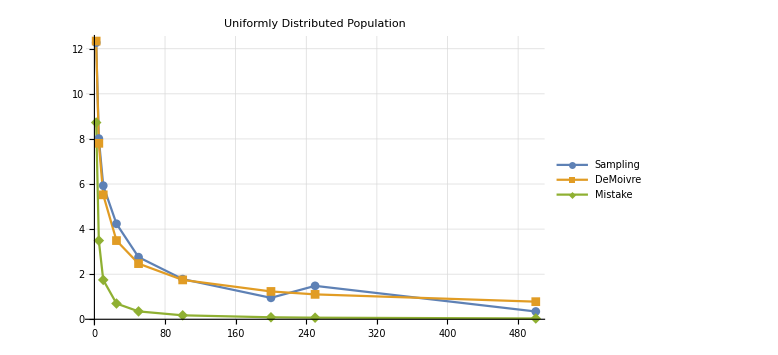

```mathematica
ListLinePlot[{stdErrorsFromSamplingUni, stdErrorsFromDeMoivreUni, stdErrorsMistakeUni}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"Sampling", "DeMoivre", "Mistake"}, Right], GridLines->Automatic, PlotLabel -> "Uniformly Distributed Population", ImageSize-> Large]
```

Amazing! The formula still gives a reasonable estimate and the mistaken estimate is even worse than the case of the normally distributed population.

## The explicit connection to the variability of small samples

To see what happens as sample sizes are decreased, let’s check what happens to the ranges of the means, standard deviations, minima and maxima of the samples. These ranges will show us how the values spread out over higher and higher ranges, thereby giving us less and less precise estimates.

```mathematica
ranges = Transpose[(calcStandardError[pHeights, #] & /@ sampleSizes)[[All,4]]]
```

{{{68.5276,69.0043},{67.9136,69.4072},{67.7199,69.9329},{66.6563,70.4188},{65.7729,70.7475},{65.5581,72.1965},{62.7776,78.4044},{59.3383,79.7128},{51.1507,87.1434}},{{9.76413,10.0821},{9.57989,10.5438},{9.43642,10.4585},{8.67619,10.6874},{7.56515,11.5131},{7.10519,13.1164},{5.29242,16.1721},{2.75389,19.6473},{0.0439273,28.3993}},{{37.5138,39.9068},{37.5138,43.4638},{37.5138,44.9927},{37.5138,50.3642},{37.5138,54.277},{37.5138,58.5171},{37.5138,66.9293},{37.5138,73.4512},{37.5138,83.7661}},{{96.0754,97.7562},{91.1373,97.7562},{91.1373,97.7562},{86.4034,97.7562},{83.3262,97.7562},{79.9937,97.7562},{74.7197,97.7562},{66.6571,97.7562},{51.9373,97.7562}}}

```mathematica
{meanRanges, stddevRanges, minRanges, maxRanges} = {ranges[[1]], ranges[[2]], ranges[[3]], ranges[[4]]}
```

{{{68.5276,69.0043},{67.9136,69.4072},{67.7199,69.9329},{66.6563,70.4188},{65.7729,70.7475},{65.5581,72.1965},{62.7776,78.4044},{59.3383,79.7128},{51.1507,87.1434}},{{9.76413,10.0821},{9.57989,10.5438},{9.43642,10.4585},{8.67619,10.6874},{7.56515,11.5131},{7.10519,13.1164},{5.29242,16.1721},{2.75389,19.6473},{0.0439273,28.3993}},{{37.5138,39.9068},{37.5138,43.4638},{37.5138,44.9927},{37.5138,50.3642},{37.5138,54.277},{37.5138,58.5171},{37.5138,66.9293},{37.5138,73.4512},{37.5138,83.7661}},{{96.0754,97.7562},{91.1373,97.7562},{91.1373,97.7562},{86.4034,97.7562},{83.3262,97.7562},{79.9937,97.7562},{74.7197,97.7562},{66.6571,97.7562},{51.9373,97.7562}}}

```mathematica
popMeans = Transpose[{sampleSizes,Table[Mean[pHeights], Length[sampleSizes]]}]
```

{{500,68.766},{250,68.766},{200,68.766},{100,68.766},{50,68.766},{25,68.766},{10,68.766},{5,68.766},{2,68.766}}

```mathematica
popStds = Transpose[{sampleSizes,Table[StandardDeviation[pHeights], Length[sampleSizes]]}]
```

{{500,9.92226},{250,9.92226},{200,9.92226},{100,9.92226},{50,9.92226},{25,9.92226},{10,9.92226},{5,9.92226},{2,9.92226}}

```mathematica
popMins = Transpose[{sampleSizes,Table[Min[pHeights], Length[sampleSizes]]}]
```

{{500,37.5138},{250,37.5138},{200,37.5138},{100,37.5138},{50,37.5138},{25,37.5138},{10,37.5138},{5,37.5138},{2,37.5138}}

```mathematica
popMaxs = Transpose[{sampleSizes,Table[Max[pHeights], Length[sampleSizes]]}]
```

{{500,97.7562},{250,97.7562},{200,97.7562},{100,97.7562},{50,97.7562},{25,97.7562},{10,97.7562},{5,97.7562},{2,97.7562}}

```mathematica
meanRanges
```

{{68.5276,69.0043},{67.9136,69.4072},{67.7199,69.9329},{66.6563,70.4188},{65.7729,70.7475},{65.5581,72.1965},{62.7776,78.4044},{59.3383,79.7128},{51.1507,87.1434}}

```mathematica
meansLow = Transpose[{sampleSizes, meanRanges[[All,1]]}]
```

{{500,68.5276},{250,67.9136},{200,67.7199},{100,66.6563},{50,65.7729},{25,65.5581},{10,62.7776},{5,59.3383},{2,51.1507}}

```mathematica
meansHigh = Transpose[{sampleSizes, meanRanges[[All,2]]}]
```

{{500,69.0043},{250,69.4072},{200,69.9329},{100,70.4188},{50,70.7475},{25,72.1965},{10,78.4044},{5,79.7128},{2,87.1434}}

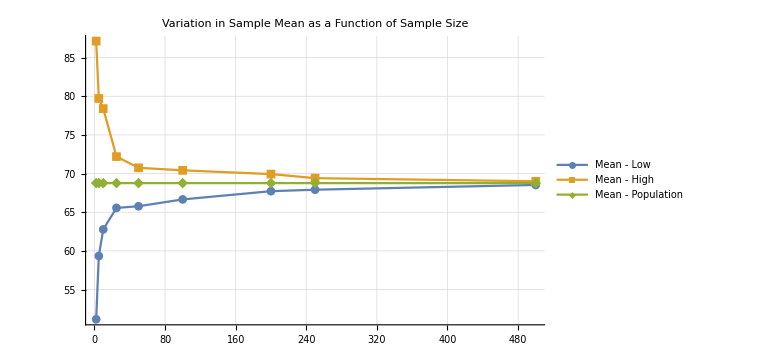

```mathematica
ListLinePlot[{meansLow, meansHigh, popMeans}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"Mean - Low", "Mean - High", "Mean - Population"}, Right], GridLines->Automatic, PlotLabel -> "Variation in Sample Mean as a Function of Sample Size", ImageSize-> Large, PlotRange-> All]
```

```mathematica
stdDevsLow = Transpose[{sampleSizes, stddevRanges[[All,1]]}]
```

{{500,9.76413},{250,9.57989},{200,9.43642},{100,8.67619},{50,7.56515},{25,7.10519},{10,5.29242},{5,2.75389},{2,0.0439273}}

```mathematica
stdDevsHigh = Transpose[{sampleSizes, stddevRanges[[All,2]]}]
```

{{500,10.0821},{250,10.5438},{200,10.4585},{100,10.6874},{50,11.5131},{25,13.1164},{10,16.1721},{5,19.6473},{2,28.3993}}

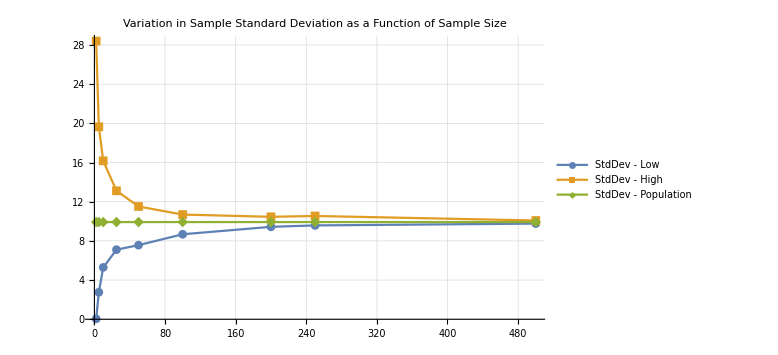

```mathematica
ListLinePlot[{stdDevsLow, stdDevsHigh, popStds}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"StdDev - Low", "StdDev - High", "StdDev - Population"}, Right], GridLines->Automatic, PlotLabel -> "Variation in Sample Standard Deviation as a Function of Sample Size", ImageSize-> Large, PlotRange-> All]
```

```mathematica
minsLow = Transpose[{sampleSizes, minRanges[[All,1]]}]
```

{{500,37.5138},{250,37.5138},{200,37.5138},{100,37.5138},{50,37.5138},{25,37.5138},{10,37.5138},{5,37.5138},{2,37.5138}}

```mathematica
minsHigh = Transpose[{sampleSizes, minRanges[[All,2]]}]
```

{{500,39.9068},{250,43.4638},{200,44.9927},{100,50.3642},{50,54.277},{25,58.5171},{10,66.9293},{5,73.4512},{2,83.7661}}

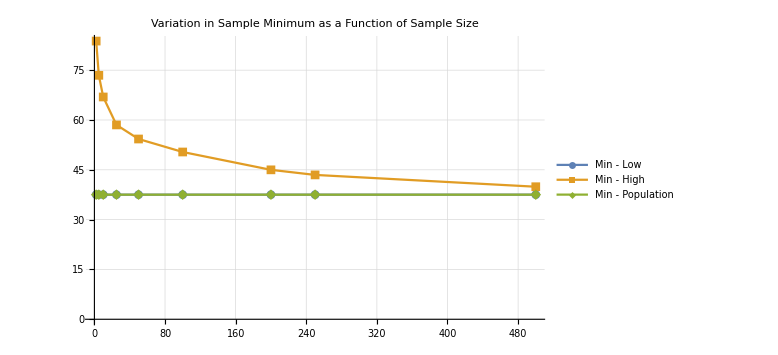

```mathematica
ListLinePlot[{minsLow, minsHigh, popMins}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"Min - Low", "Min - High", "Min - Population"}, Right], GridLines->Automatic, PlotLabel -> "Variation in Sample Minimum as a Function of Sample Size", ImageSize-> Large, PlotRange-> All]
```

```mathematica
maxsLow = Transpose[{sampleSizes, maxRanges[[All,1]]}]
```

˚˚3{50,83.3262},{25,79.9937},{10,74.7197},{5,66.6571},{2,51.9373}}

```mathematica
maxsHigh = Transpose[{sampleSizes, maxRanges[[All,2]]}]
```

{{500,97.7562},{250,97.7562},{200,97.7562},{100,97.7562},{50,97.7562},{25,97.7562},{10,97.7562},{5,97.7562},{2,97.7562}}

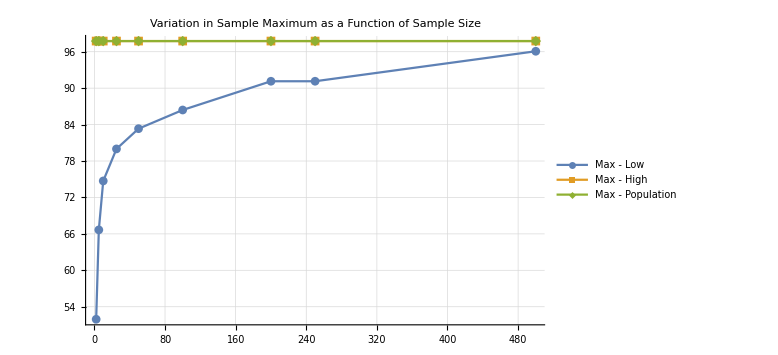

```mathematica
ListLinePlot[{maxsLow, maxsHigh, popMaxs}, PlotMarkers -> Automatic, PlotLegends-> Placed[{"Max - Low", "Max - High", "Max - Population"}, Right], GridLines->Automatic, PlotLabel -> "Variation in Sample Maximum as a Function of Sample Size", ImageSize-> Large, PlotRange-> All]
```